```mathematica
n = 3;
m = 3;
```

```mathematica
ky=n*Pi/4;
kx=m*Pi/3;
kz = 1;
z=0;
```

```mathematica
Sin[(π x)/3] Sin[(π y)/4]
```

Sin[(π x)/3] Sin[(π y)/4]

```mathematica
Plot3D[ Sin[kx*x]*Sin[ky*y]*Exp[Im[kz*z]],{x,0.,6.},{y,0.,4.}]
```

-Graphics3D-

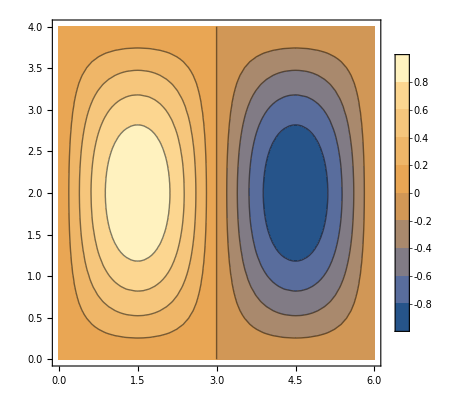
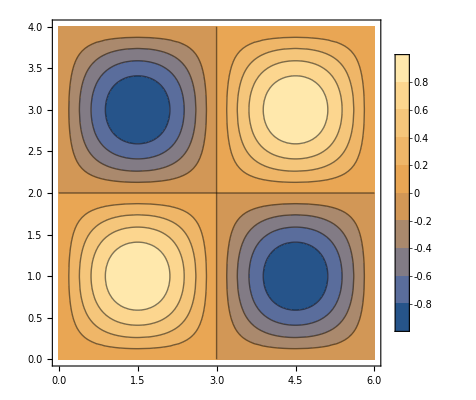
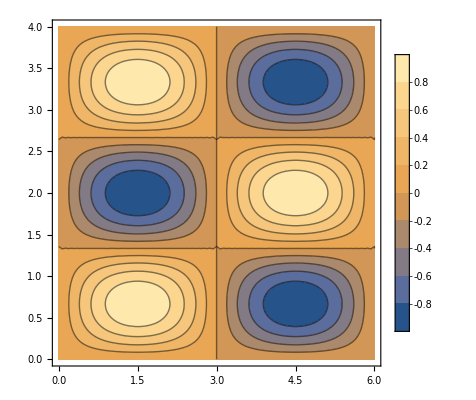
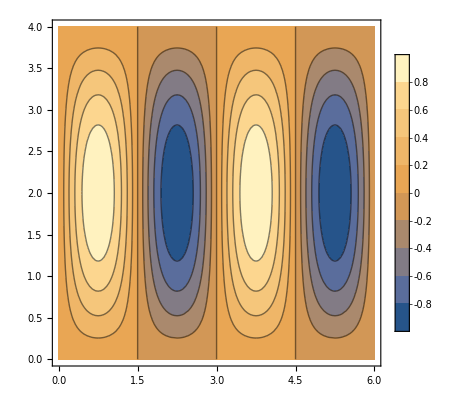
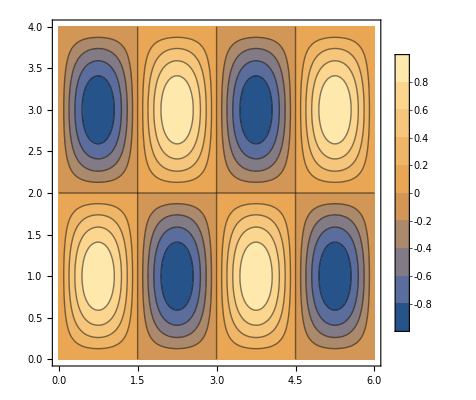
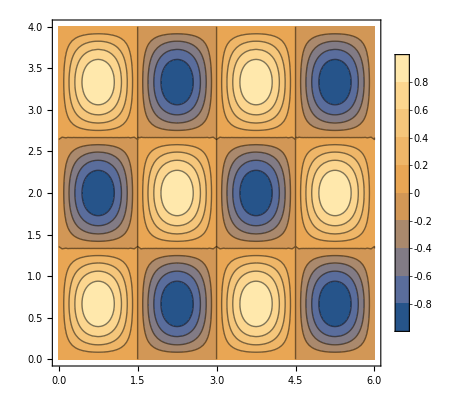
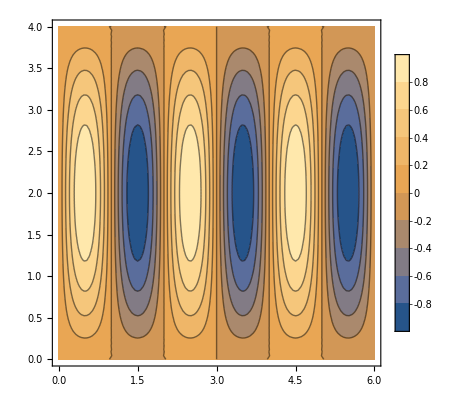
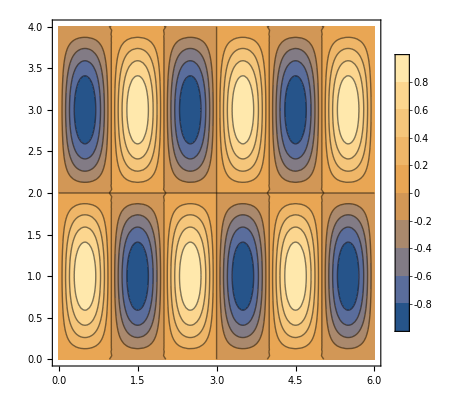
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ContourPlot[Sin[(m Pi/3) x] Sin[(n Pi/4) y],{x,0,6},{y,0,4},PlotLegends->Automatic],{m,3},{n,3}]
```

```mathematica
(**)
```